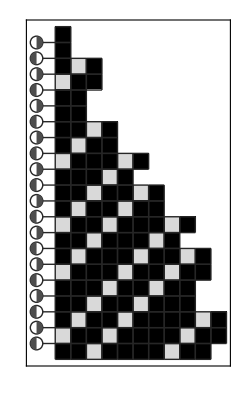

```mathematica
With[{hist=ResourceFunction["CyclicTagSystem"][{{1},{1,0,1}},{1},20],icon=Function[{pos,r,phase},{GrayLevel[.15],Circle[pos,r],GrayLevel[.3],Disk[pos,r,{Pi/2,3Pi/2}+phase π]}]},Show[{Graphics[ArrayPlot[hist,]],Graphics[Table[With[{pos={-1.2,Length[hist]-i}},{icon[pos,.4,Mod[i,2]],GrayLevel[.15],Line[{pos+{.4,0},pos+{1.2,0}}]}],{i,Length[hist]-1}],]},]]
```